```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* cf: A073058*)
```

```mathematica
(* F. M. Dekking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.15*)
```

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
Clear[z]
```

```mathematica
m=Transpose[CompanionMatrix[2-5 z+5 z^3-z^5,z] ]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{2,-5,0,5,0}}

```mathematica
name={"Cycle",5}
```

{Cycle,5}

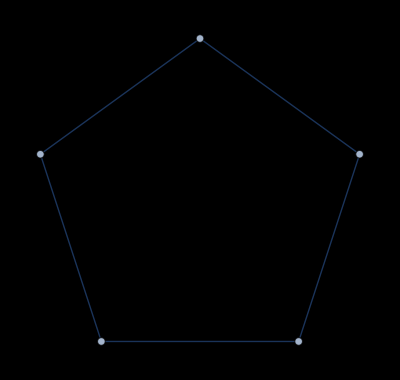

```mathematica
Show[GraphData[name,"Graph","MinimalCrossing"],ImageSize->Full,Background->Black]
```

```mathematica
GraphPlot3D[GraphData[name],ImageSize->Full,Background->Black]
```

-Graphics3D-

```mathematica
m=AdjacencyMatrix[GraphData[name]]
```

SparseArray[…]

```mathematica
n0=5
```

5

```mathematica
p0[z_]=CharacteristicPolynomial[AdjacencyMatrix[GraphData[name]],z]
```

2-5 z+5 z^3-z^5

```mathematica
AdjacencyGraph[m,ImageSize->Full,PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
(* make polynomial*)
```

```mathematica
Factor[Det[m-x*IdentityMatrix[n0]]]
```

-((-2+x) (-1+x+x^2)^2)

```mathematica
(* solve Polynomial*)
```

```mathematica
z=x/.NSolve[CharacteristicPolynomial[m,x]==0,x][[1]]
```

-1.61803

```mathematica
v=Table[N[{Cos[2*Pi*i/5],Sin[2*Pi*i/5]}],{i,5}]
```

{{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1.,0.}}

```mathematica
rule=NSolve[CharacteristicPolynomial[m,x]==0,x][[1]]
```

```mathematica
Clear[s]
ss=Table[Union[Table[If[m[[i,j]]==1||j==i,j,Nothing],{j,5}]],{i,5}]
```

{{1,2,5},{1,2,3},{2,3,4},{3,4,5},{1,4,5}}

```mathematica
Table[s[i]=ss[[i]],{i,5}]
```

{{1,2,5},{1,2,3},{2,3,4},{3,4,5},{1,4,5}}

```mathematica
w=Join[Flatten[Table[s[i],{i,5}]],Reverse[Flatten[Table[s[i],{i,5}]]]]
```

{1,2,5,1,2,3,2,3,4,3,4,5,1,4,5,5,4,1,5,4,3,4,3,2,3,2,1,5,2,1}

```mathematica
t[a_] :=Flatten[s/@a];         
p[0]={1};p[1]=t[p[0]];
p[n_]:=t[p[n-1]]
aa=p[5];
```

```mathematica
Length[aa]
```

243

```mathematica
(* second chord transform*)
```

```mathematica
(* pentatonic:BlackKeys{Db,Eb,Gb,Ab,Bb}*)
```

```mathematica
(*Cminor:https://www.pianoscales.org/pentatonic.html*)
```

```mathematica
v={1,3,6,8,10,1,3,6,8,10}
```

{1,3,6,8,10,1,3,6,8,10}

```mathematica
PiDigits=Table[v[[aa[[i]]]],{i,Length[aa]}]
```

{1,3,10,1,3,6,1,8,10,1,3,10,1,3,6,3,6,8,1,3,10,6,8,10,1,8,10,1,3,10,1,3,6,1,8,10,1,3,10,1,3,6,3,6,8,1,3,6,3,6,8,6,8,10,1,3,10,1,3,6,1,8,10,3,6,8,6,8,10,1,8,10,1,3,10,6,8,10,1,8,10,1,3,10,1,3,6,1,8,10,1,3,10,1,3,6,3,6,8,1,3,10,6,8,10,1,8,10,1,3,10,1,3,6,1,8,10,1,3,10,1,3,6,3,6,8,1,3,6,3,6,8,6,8,10,1,3,10,1,3,6,3,6,8,1,3,6,3,6,8,6,8,10,3,6,8,6,8,10,1,8,10,1,3,10,1,3,6,1,8,10,1,3,10,1,3,6,3,6,8,1,3,10,6,8,10,1,8,10,1,3,6,3,6,8,6,8,10,3,6,8,6,8,10,1,8,10,1,3,10,6,8,10,1,8,10,1,3,10,1,3,6,1,8,10,3,6,8,6,8,10,1,8,10,1,3,10,6,8,10,1,8,10}

```mathematica
SeedRandom[123]
```

```mathematica
snd1=Sound[Table[SoundNote[RandomChoice[{"HighWoodblock","Snare","Sticks","SideStick","BassDrum","MidTom","LowBongo","LowTom","LowWoodblock"}],.24],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_1.mid",snd1]
```

```mathematica
snd2=Sound[Table[SoundNote[PiDigits[[i]],.24,"Piano"],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_2.mid",snd2]
```

```mathematica
snd2a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,"SynthBass2"],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_2a.mid",snd2a]
```

```mathematica
(* 8th notes*)
snd10=Sound[Table[SoundNote[PiDigits[[i]]+24,.24,"Flute"],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_10.mid",snd10]
```

```mathematica
snd3=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,RandomChoice[If[Mod[i,5]>0,{"Bass","ElectricBass","BassAndLead","PickedBass"},{"SynthBass2"}]]],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_3.mid",snd3]
```

```mathematica
w0={"Bass","ElectricBass","BassAndLead","PickedBass","SynthBass2"};
```

```mathematica
snd3a=Sound[Table[SoundNote[PiDigits[[i]]-24,.24,w0[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_3a.mid",snd3a]
```

```mathematica
w1={"AltoSax","ElectricGuitar","Piano","Banjo","Whistle"};
```

```mathematica
snd4a=Sound[Table[SoundNote[PiDigits[[i]],.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_4a.mid",snd4a]
```

```mathematica
snd4b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.24,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_4b.mid",snd4b]
```

```mathematica
snd5b=Sound[Table[SoundNote[{PiDigits[[i]],PiDigits[[i]]+3},.48,w1[[1+Mod[i,5]]]],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_5b.mid",snd5b]
(* quarter notes*)
```

```mathematica
snd5=Sound[Table[SoundNote[PiDigits[[i]]+24,.48,"Tinklebell"],{i,Floor[Length[PiDigits]/2]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_5.mid",snd5]
```

```mathematica
snd6=Sound[Table[SoundNote[PiDigits[[i]]-24,0.48,"SynthBass2"],{i,Floor[Length[PiDigits]/2]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_6.mid",snd6]
```

```mathematica
snd13=Sound[Table[SoundNote[PiDigits[[i]]+12,.20,"Piano"],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_13.mid",snd13]
```

```mathematica
snd14=Sound[Table[SoundNote[PiDigits[[i]]-24,.20,"SynthBass2"],{i,Length[PiDigits]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_14.mid",snd14]
```

```mathematica
wa={0.96,0.24,0.24,0.24,0.24,0.96,0.24,0.24,0.48,0.96,0.12,0.12,0.12,0.12};
```

```mathematica
Apply[Plus,wa]
```

5.28

```mathematica
snd8=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_8.mid",snd8]
```

```mathematica
wb={4*0.24,0.24,0.24,0.24,0.24,0.48,0.48,0.48,0.48,0.24,0.24,0.24,0.24,0.48,0.48};
```

```mathematica
Apply[Plus,wb]
```

5.76

```mathematica
snd4c=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_4c.mid",snd4c]
```

```mathematica
snd5c=Sound[Table[SoundNote[PiDigits[[i]]-24,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_5c.mid",snd5c]
```

```mathematica
Clear[wa,wb]
```

```mathematica
wa={0.12,0.12,0.12,0.12,0.24,0.24,0.48,0.48,0.24,0.24,0.24,0.24};
```

```mathematica
Apply[Plus,wa]
```

2.88

```mathematica
snd9=Sound[Table[SoundNote[RandomChoice[{"Snare","Sticks","BassDrum","Claves","MidTom","LowBongo","LowTom"}],wa[[1+Mod[i,Length[wa]]]]],{i,Floor[Length[PiDigits]/2]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_9.mid",snd9]
```

```mathematica
wb={4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,3*0.24,0.12,0.12,0.12,0.12};
```

```mathematica
Apply[Plus,wb]
```

4.08

```mathematica
snd4d=Sound[Table[SoundNote[PiDigits[[i]],wa[[1+Mod[i,Length[wa]]]],"Piano"],{i,Ceiling[Length[PiDigits]]}]]
Export["black_keychords_5symbol_substitution_BlackKeys_level5_4d.mid",snd4d]
snd5d=Sound[Table[SoundNote[PiDigits[[i]]-24,wb[[1+Mod[i,Length[wb]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_5d.mid",snd5d]
```

$Failed

```mathematica
wc={4*0.24,0.24,0.24,0.24,0.24,4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,2*0.48,4*0.24,0.24,0.24,0.24,0.24,4*0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,0.24,2*0.48};
```

```mathematica
Apply[Plus,wc]
```

13.44

```mathematica
w1={None,"Piano",None,"Piano",None,None,"Piano","Piano",None,None,"Piano","Piano",None,"Piano",None,"Piano",None,"Piano"};
```

```mathematica
snd4f=Sound[Table[SoundNote[{PiDigits[[i]]-5,PiDigits[[i]],PiDigits[[i]]+3},wc[[1+Mod[i,Length[wc]]]],w1[[1+Mod[i,8]]]],{i,Ceiling[Length[PiDigits]]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_4f.mid",snd4f]
```

```mathematica
snd5f=Sound[Table[SoundNote[{PiDigits[[i]]-5-12,PiDigits[[i]]-12,PiDigits[[i]]+3-12},wc[[1+Mod[i,Length[wc]]]],"SynthBass2"],{i,Ceiling[Length[PiDigits]]}]]
Export["Cycle5Graph_5symbol_substitution_BlackKeys_level5_5f.mid",snd5f]
```

```mathematica
(*end*)
```